```mathematica
DSolve[D[f[r],{r,2}]+1/r f'[r]-(κ^2)f[r]==0,f[r],r]
```

{{f[r]→BesselJ[0,ⅈ r κ] C[1]+BesselY[0,-ⅈ r κ] C[2]}}

```mathematica
BesselI[n,0]
```

BesselI[n,0]

```mathematica
BesselK[n,0]
```

BesselK[n,0]

```mathematica
BesselI[0,0]
```

1

```mathematica
BesselK[0,0]
```

∞

```mathematica
BesselI[2,0]
```

0

```mathematica
BesselI[-3,0]
```

0

```mathematica
BesselK[2,0]
```

ComplexInfinity

```mathematica
BesselK[-1,0]
```

ComplexInfinity

```mathematica
Block[
{f,r,θ,B0},
f[r_,θ_]:=B0 Cos[θ];
FullSimplify[D[f[r,θ],{r,2}]+1/r D[f[r,θ],r]+1/r^2D[f[r,θ],{θ,2}]]
]
```

-(B0 Cos[θ])/r^2

```mathematica
Integrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],θ]
```

∫ⅇ^(ⅈ (-k+m) θ) BesselI[m,(R Sec[θ] (1+Tan[θ]^n)^(-1/n))/λ]ⅆθ

```mathematica
Integrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π}]
```

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.55186}. NIntegrate obtained -5.54381×10^-9-0.000575968 ⅈ and 0.00451422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 5.90877×10^-8-0.000016731 ⅈ and 0.000469258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.796988}. NIntegrate obtained 1.83639×10^-8-0.0000288421 ⅈ and 0.000486714 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

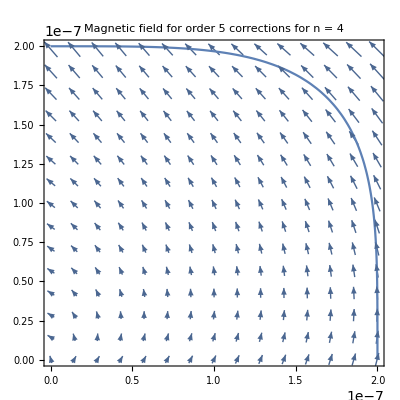

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=5;(* Scale of the number of coefficients *)
n=4;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.55186}. NIntegrate obtained -5.54381×10^-9-0.000575968 ⅈ and 0.00451422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 1.81464×10^-11-9.85624×10^-10 ⅈ and 5.2804×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 4.12716×10^-7+1.49956×10^-9 ⅈ and 5.50395×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

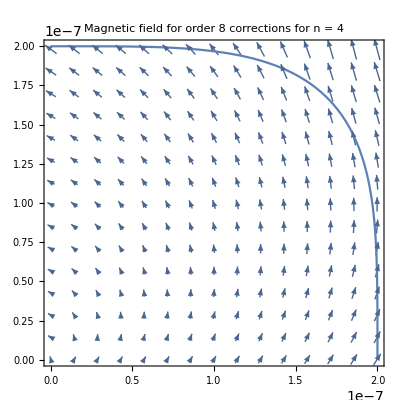

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=8;(* Scale of the number of coefficients *)
n=4;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.55186}. NIntegrate obtained -5.54381×10^-9-0.000575968 ⅈ and 0.00451422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 5.40801×10^-15+1.30652×10^-10 ⅈ and 7.82397×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -1.49235×10^-11+4.73439×10^-9 ⅈ and 1.56492×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

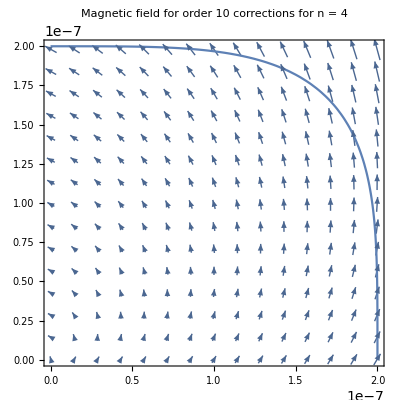

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=10;(* Scale of the number of coefficients *)
n=4;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.61982}. NIntegrate obtained -2.3879×10^-8-0.000581647 ⅈ and 0.00538842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 6.47982×10^-8-0.000017387 ⅈ and 0.000500983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.3187}. NIntegrate obtained 1.94505×10^-8-0.0000297695 ⅈ and 0.000619748 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

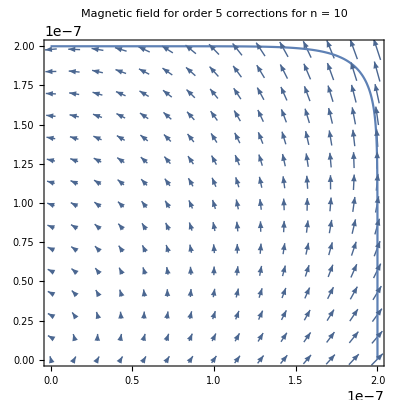

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=5;(* Scale of the number of coefficients *)
n=10;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.61982}. NIntegrate obtained -2.3879×10^-8-0.000581647 ⅈ and 0.00538842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained -2.28795×10^-12+1.26574×10^-8 ⅈ and 9.66895×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.42021×10^-10+3.38813×10^-21 ⅈ and 0.0000139444 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

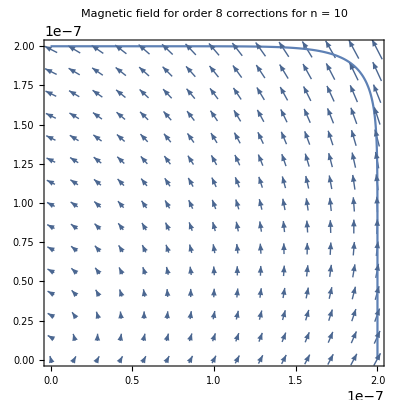

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=8;(* Scale of the number of coefficients *)
n=10;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.98767}. NIntegrate obtained -2.39715×10^-8-0.000581659 ⅈ and 0.00594167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.54619}. NIntegrate obtained 5.80158×10^-8-0.000054305 ⅈ and 0.000764385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.18202×10^-6-0.000997531 ⅈ and 0.0101573 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

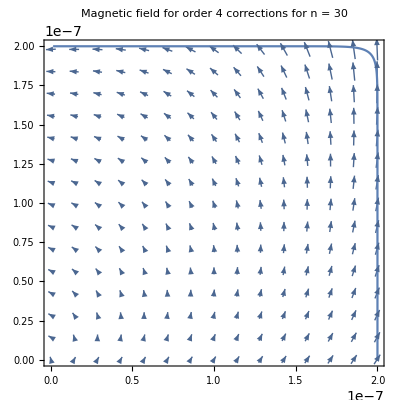

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=4;(* Scale of the number of coefficients *)
n=30;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.98767}. NIntegrate obtained -2.39715×10^-8-0.000581659 ⅈ and 0.00594167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.53392}. NIntegrate obtained -2.25026×10^-12+1.26589×10^-8 ⅈ and 1.2327×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.42853×10^-10+3.04932×10^-20 ⅈ and 0.0000137432 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

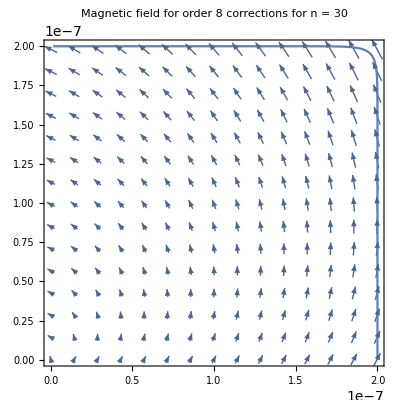

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=8;(* Scale of the number of coefficients *)
n=30;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.98767}. NIntegrate obtained -2.39715×10^-8-0.000581659 ⅈ and 0.00594167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -1.42404×10^-11+5.06074×10^-9 ⅈ and 2.10063×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.53392}. NIntegrate obtained -2.25026×10^-12+1.26589×10^-8 ⅈ and 1.2327×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

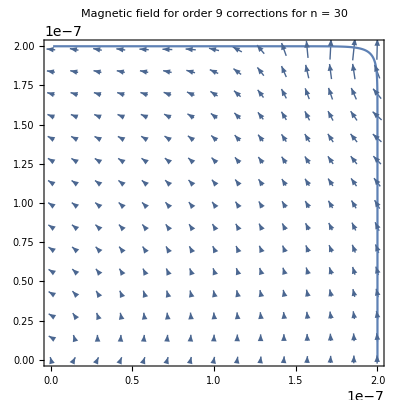

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=9;(* Scale of the number of coefficients *)
n=30;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.54619}. NIntegrate obtained -2.39715×10^-8-0.000581659 ⅈ and 0.00606573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.96312}. NIntegrate obtained 6.85193×10^-8-0.0000583563 ⅈ and 0.000805879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.18202×10^-6-0.000997531 ⅈ and 0.0102704 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

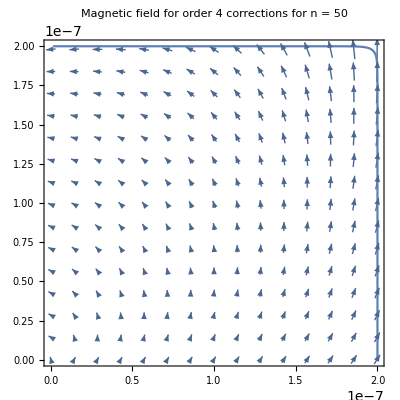

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=4;(* Scale of the number of coefficients *)
n=50;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.54619}. NIntegrate obtained -2.39715×10^-8-0.000581659 ⅈ and 0.00606573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 6.4821×10^-8-0.0000173883 ⅈ and 0.000509701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.96312}. NIntegrate obtained 6.85193×10^-8-0.0000583563 ⅈ and 0.000805879 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

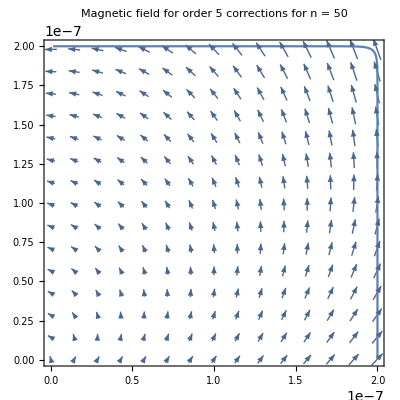

```mathematica
Block[
{M,R,λ,n,Ja,Jb,θ,Br,Bθ,B0,eqn,soln,p,q},
M=5;(* Scale of the number of coefficients *)
n=50;(* Curvature exponent *)
R=200*10^(-9);(* Size of the conveyor belt cavity *)
λ=110*10^(-9);(* London penetration depth of MgB2 (magnesium diboride) in 4.8 mT and 10.8 K *)
B0=4.8*10^(-3);(* Central magnetic field B0 = 4.8 mT *)
Ja[m_,k_]:=NIntegrate[BesselI[m,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[I(m-k)θ],{θ,0,2π},Method->"RiemannRule"];
Jb[k_]:=NIntegrate[BesselI[0,R/λ Sec[θ]/(1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},Method->"RiemannRule"];
eqn=Table[Jb[k]B0/2+Total[Drop[Table[p[m]Ja[m,k],{m,-M,M}],{M+1}]]==0,{k,1,2M}];
soln=NSolve[eqn,Drop[Table[p[m],{m,-M,M}],{M+1}]];
Br[x_,y_]:=Part[B0/2BesselI[0,Sqrt[x^2+y^2]/λ]+Total[Drop[Table[p[m]BesselI[m,Sqrt[x^2+y^2]/λ]Exp[I m ArcTan[x,y]],{m,-M,M}],{M+1}]]/.soln,1];
Bθ[x_,y_]:=Sqrt[3]B0/2BesselI[0,Sqrt[x^2+y^2]/λ];
Show[VectorPlot[{Re[(Br[x,y] x-Bθ[x,y] y)/Sqrt[x^2+y^2]],Re[(Br[x,y] y+Bθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.990R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Magnetic field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```